#### Kamen setup

```mathematica
kamen[x_]:=0.96-0.25(x-0.5)^2
FindRoot[kamen[x],{x,-2}]
```

{x→-1.45959}

```mathematica
{x->-1.4595917942265424}
```

```mathematica
{x->2.4595917942265424}
```

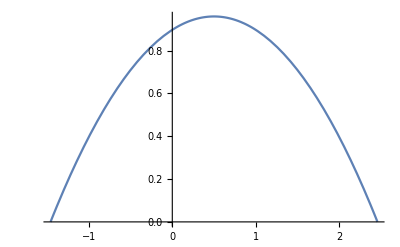

```mathematica
kamenPlot=Plot[kamen[x],{x,-1.4595917942265424,2.4595917942265424}]
```

#### String setup

```mathematica
k=1;
g=-1;
boundaryHeightLeft=1;
boudaryHeightRight=1;
boundaryLeft =-1;
boundaryRight=2;
nXPoints=60; (* Tu klameme, nepocitame totiz bod v "boudaryLeft". Takze oficialne este je o jeden bod naviac. *)

(* Finite difference method - rozdelime x-ovu os na bodiky, v tychto bodoch pocitame "y" *)
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```

Toto navadza na sustavu rovnic -> matica*y=hodnoty, kde pozname maticu a hodnoty: (vid text)

```mathematica
(* Opisanie matice a vektora podla textu *)
matica = 1/dx^2* Table[If[i==j,2, If[Abs[i-j]==1,-1,0]],{i,0,nXPoints},{j,0,nXPoints}];
hodnoty = Table[-1+If[i==0 || i==nXPoints,1/dx^2,0],{i,0,nXPoints}];

(* Sustavu treba vyriesit. Kedze je to ilustracne, tak pouzivam LinearSolve, ale inak by sme to mali robit prave asi tym Newtonom, alebo ako. *)
ypsilony = LinearSolve[matica,hodnoty];
```

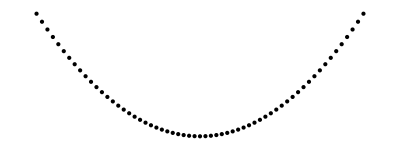

```mathematica
(* Transpose[{xPoints,ypsilony}]; *)
(* Previsnute body bez väzieb. *)
body = Graphics[Point[Transpose[{xPoints,ypsilony}]]]
```

#### Praca s kamenom a String-om - funguje tu zatial iba ten PLOT, kam by sme mohli hodit vsetky veci dokopy.

```mathematica
psi[y_]:=1/2*k*(D[y,x])^2-g*y;
potential[y_]:=Integrate[psi[y],{x,0,1}];
psi[y[x]];
potential[y[x]];
```

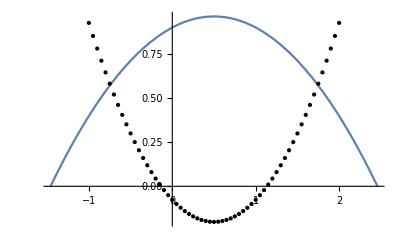

```mathematica
Show[kamenPlot, body, PlotRange->All]
```